## Calculating infinite-temperature autocorrelation functions via Taylor expansion

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
H={{1,{σx,σx}},{hz,{σz}},{hx,{σx}}}; (* Hamiltonian *)
A={{1,{σz}}}; (* observable *)

nmax=28;

Clear[Mtable]
SetDirectory[NotebookDirectory[]]; (* defines a directory *)
Mtable=Import["6 - moments_Ising.mx"]; (* the first element is for n=1 *)
Length[Mtable]==2nmax

For[i=1,i≤nmax,i++,
res = Mtable[[2*i]];
(*Print[i," ",Length[res]];*)
If[Length[res]<=20,Print[res]]
];
```

True

8+4 hx^2

128+192 hx^2+16 hx^4+128 hz^2+16 hx^2 hz^2

2048+7680 hx^2+1920 hx^4+64 hx^6+6144 hz^2+5888 hx^2 hz^2+128 hx^4 hz^2+2048 hz^4+64 hx^2 hz^4

32768+229376 hx^2+143360 hx^4+14336 hx^6+256 hx^8+196608 hz^2+589824 hx^2 hz^2+125952 hx^4 hz^2+768 hx^6 hz^2+196608 hz^4+130560 hx^2 hz^4+768 hx^4 hz^4+32768 hz^6+256 hx^2 hz^6

524288+5898240 hx^2+6881280 hx^4+1720320 hx^6+92160 hx^8+1024 hx^10+5242880 hz^2+32129024 hx^2 hz^2+22470656 hx^4 hz^2+2146304 hx^6 hz^2+4096 hx^8 hz^2+10485760 hz^4+27107328 hx^2 hz^4+4153344 hx^4 hz^4+6144 hx^6 hz^4+5242880 hz^6+2623488 hx^2 hz^6+4096 hx^4 hz^6+524288 hz^8+1024 hx^2 hz^8

```mathematica
(*
scp filipp@10.30.16.102:/data1/filipp/grid-commutators-2/io/mt-dxa.zip.
rm-rf mt-dxa;mkdir mt-dxa;unzip mt-dxa.zip-d mt-dxa;cd mt-dxa
for f in* ;do sed-i':a;N;$!ba;s/\n//g;' $f;sed-i's/i_/ii/g;s/ //g;s|\\||g;' $f;echo-n $f;done
*)
Clear[Mtable];
Mtable={};
nmax=45
For[i=1,i≤nmax,i++,
file = OpenRead["mt-dxa\\out-"<>ToString[i]<>".mt"]; res = Read[file]; Close[file];
res=res/.ii->1;
AppendTo[Mtable,0];
AppendTo[Mtable,res];
Print[i," ",Length[res]];
If[Length[res]<=20,Print[res]]
];
```

45

1 2

8+4 hx^2

2 5

128+192 hx^2+16 hx^4+128 hz^2+16 hx^2 hz^2

3 9

2048+7680 hx^2+1920 hx^4+64 hx^6+6144 hz^2+5888 hx^2 hz^2+128 hx^4 hz^2+2048 hz^4+64 hx^2 hz^4

4 14

32768+229376 hx^2+143360 hx^4+14336 hx^6+256 hx^8+196608 hz^2+589824 hx^2 hz^2+125952 hx^4 hz^2+768 hx^6 hz^2+196608 hz^4+130560 hx^2 hz^4+768 hx^4 hz^4+32768 hz^6+256 hx^2 hz^6

5 20

524288+5898240 hx^2+6881280 hx^4+1720320 hx^6+92160 hx^8+1024 hx^10+5242880 hz^2+32129024 hx^2 hz^2+22470656 hx^4 hz^2+2146304 hx^6 hz^2+4096 hx^8 hz^2+10485760 hz^4+27107328 hx^2 hz^4+4153344 hx^4 hz^4+6144 hx^6 hz^4+5242880 hz^6+2623488 hx^2 hz^6+4096 hx^4 hz^6+524288 hz^8+1024 hx^2 hz^8

6 27

7 35

8 44

9 54

10 65

11 77

12 90

13 104

14 119

15 135

16 152

17 170

18 189

19 209

20 230

21 252

22 275

23 299

24 324

25 350

26 377

27 405

28 434

29 464

30 495

31 527

32 560

33 594

34 629

35 665

36 702

37 740

38 779

39 819

40 860

41 902

42 945

43 989

44 1034

45 1080

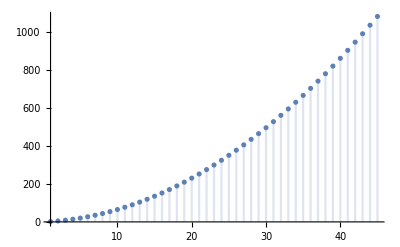

```mathematica
DiscretePlot[Length[Mtable[[2i]]],{i,1,45}]
```

```mathematica
mm={12,480,25984,1694208,127258624,10783342592,1019673509888,107060323680256,12469034121428992,1613762515315982336,232736621970029805568,37468646645944075419648,6726394693098760675786752,1340433610285320688734568448,294391435294882867890188451840,70659698635880317667608199430144,18383424921170050832257258778263552,5147501922089241875609891362536685568,1542402400283276113669614948668265201664,492432525422001580271341582388177351475200,166985805198508106978965686562725967100379136,60011852488095956067395190665735924993040056320,22821321744324019152247154618657381361730948431872,9172207374041781749043802673339425314176975748726784,3892052853514868229060585022861205953766446860739805184,1741736488569588529172771998235278437950082051065922977792,821019133269536743838893539994338673397100678325485105577984,407086843763398331397385204208407255958886525287040747053252608,211990829889808789195437699387039831255135134538810758197371994112,115754651941408887232253140259122456149371760683740727687331373383680,66166596237703872256126915723522220984465097504279554678985792092635136,39530072936257449901374525090449349559603851447100658065034700516313006080,24646757783977889749525872721004379593240131044109640793744075941140506869760,16015858109930051337482877843244494350822380543617937802711923518036880757096448,10833753072406488462262074132859724923839003624262790509360495364480719760857759744,7620581541304124813656489403945273131158245029661872172588240591095613039962778238976,5568944585532111508410499104658395233823379770020424361966461875062472358794201533513728,4224439735905136953825989317559917466695928508761395026089245710815314351095999194227277824,3323843247775625289903213303600983380005695346567953993918161657219885198513483978643486015488,2710613205308213119249609362155540213052003237873428947613674131447949025132969096999139593420800,2289489892850970408834540810440144834655617422363836454740677715045134451758621541567258816170426368,2001453495607268189063620952290269505902583051218882018390254310106562921877530480766976590064753049600,1809588827470560013981821635403092794798688775869840545515811131487657718540062168703067251339768165826560,1690965881301974315742920976115923524679163918473093378650811739823130238133010125201239580988275912104476672,1631947281186195458585922089426638344862963746050865479659865349026178052058243485365527768435580960161017102336};
```

```mathematica
diff=Table[If[(Mtable/.{hx->1,hz->1})[[2i]]!=mm[[i]],i,0],{i,1,nmax}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
a[0]=1;
Print[nmax];
Monitor[
Do[
a[2n-1]=0;
a[2n]=(-1)^n/((2n)!)Mtable[[2n]],
{n,1,nmax}],
n]; (* coefficients of Taylor expansion *)

a[8] (* example *)
```

45

(32768+229376 hx^2+143360 hx^4+14336 hx^6+256 hx^8+196608 hz^2+589824 hx^2 hz^2+125952 hx^4 hz^2+768 hx^6 hz^2+196608 hz^4+130560 hx^2 hz^4+768 hx^4 hz^4+32768 hz^6+256 hx^2 hz^6)/40320

```mathematica
P45[t]/.{hx->1,hz->1}
```

P45[t]

```mathematica
P27[t_]:=1+Sum[a[2n] t^(2n),{n,1,27}]//N;
P28[t_]:=1+Sum[a[2n] t^(2n),{n,1,28}]//N;
P44[t_]:=1+Sum[a[2n] t^(2n),{n,1,44}]//N;
P45[t_]:=1+Sum[a[2n] t^(2n),{n,1,45}]//N;
Manipulate[
Show[
Plot[{Evaluate[P27[t]/.{hx->hhx,hz->hhz}],
Evaluate[P28[t]/.{hx->hhx,hz->hhz}],
Evaluate[P44[t]/.{hx->hhx,hz->hhz}],
Evaluate[P45[t]/.{hx->hhx,hz->hhz}]
},{t,0.01,3},PlotRange->{-1.05,1.05},AxesLabel->{"t","C(t)"}],
Plot[{Evaluate[(P45[t]-P44[t])/.{hx->hhx,hz->hhz}],
Evaluate[(P28[t]-P27[t])/.{hx->hhx,hz->hhz}]
},{t,0.01,3},PlotRange->{-1.05,1.05},PlotStyle->Red]
],
{{hhx,1},0,2},
{{hhz,1},0,2}
]
```

## Calculating out-of-equilibrium dynamics of an observable via Taylor expansion

```mathematica
ToString/@{5}
```

{5}

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]]; (* defines a directory *)

H={{1,{σx,σx}},{hz,{σz}},{hx,{σx}}}; (* Hamiltonian *)

dX[0]={{1,{σz}}}; (* Observable *)

nmax=21;

Monitor[
Do[
dX[n]=Import["Isinhxhz_sigmaz_n"<>ToString/@{n}<>".mx"],
{n,1,nmax}
],n
];

Monitor[
Do[
(* Print["n=",n]; *)
timing=AbsoluteTiming[
a[n]=1/(n!)Apply[Plus,
Apply[
Times,
(dX[n][[All,2]]/.id->1),2
]
*dX[n][[All,1]]//Simplify
]][[1]],
(* Print["time of calculation (min)",timing/60],*)
{n,0,21}],
n];
timing
```

85.5743

```mathematica
dX[1]
```

{{2 hx,{σy}},{2,{σx,σy}},{2,{σy,σx}}}

```mathematica
dX[2]
```

{{4 hx hz,{σx}},{-4 (2+hx^2),{σz}},{8 hz,{σx,σx}},{-8 hx,{σx,σz}},{-8 hz,{σy,σy}},{-8 hx,{σz,σx}},{-8,{σx,σz,σx}}}

```mathematica
a[1]//Expand
```

2 hx σy+4 σx σy

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nmax=45;
a[0]=σz;(* Observable *)
For[i=1,i≤nmax,i++,
file = OpenRead["mt-dxa\\out-"<>ToString[i]<>".dxa"]; res = Read[file]; Close[file];
a[i]=(res/.{ii->I,S[x_]:>x,koef[x_]:>x}/.{cx->σx,cy->σy,cz->σz})I^i/i!//Expand
]
```

```mathematica
a[6]/.{hx->1,hz->1,σx->3/5,σy->0,σz->4/5}
```

-5248808/140625

```mathematica
AbsoluteTiming[Do[
aa[n]=a[n]/.{hx->1.,hz->1.,σx->3./5,σy->0.,σz->4./5},
{n,0,nmax}
]]
```

{3.5422,Null}

```mathematica
aa[10]
```

-17666507648/1107421875

```mathematica
Sum[aa[n] t^n,{n,0,21}]
```

4/5-(894 t^2)/125+(43856 t^4)/1875-(5248808 t^6)/140625+(176706296 t^8)/4921875-(17666507648 t^10)/1107421875-(1919753581888 t^12)/182724609375+(2250632005397824 t^14)/83139697265625-(178027118237059904 t^16)/6235477294921875+(99052710970424129792 t^18)/4770140130615234375-(25680266688936817378048 t^20)/2265816562042236328125

```mathematica
myPlot[hhx_,hhz_,px_,py_,pz_]:=Module[{
},
Do[
aa[n]=a[n]/.{hx->hhx,hz->hhz,σx->px,σy->py,σz->pz},
{n,0,nmax}
];
Plot[{Sum[aa[n] t^n,{n,0,45}],Sum[aa[n] t^n,{n,43,45}]},{t,0,3},PlotRange->{-1.05,1.05}]
]
```

```mathematica
Sum[aa[n] t^n,{n,43,45}]
```

-(99199823365901710360149554330352457815633545664877362176 t^44)/72052595411052480779484733815736264572478830814361572265625

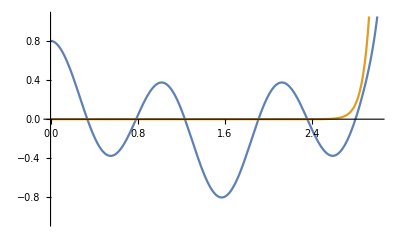

```mathematica
myPlot[1,0,3/5,0,4/5]
```

```mathematica
yourPlot[hhx_,hhz_,px_,py_,pz_]:=Module[{
},
Do[
aa[n]=a[n]/.{hx->hhx,hz->hhz,σx->px,σy->py,σz->pz},
{n,0,nmax}
];
Plot[{Sum[aa[n] t^n,{n,0,21}],Sum[aa[n] t^n,{n,0,19}]},{t,0,3},PlotRange->{-1.05,1.05}]
]
```

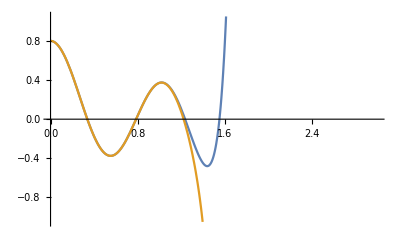

```mathematica
yourPlot[1,0,3/5,0,4/5]
```

```mathematica
Manipulate[
Do[
aa[n]=a[n]/.{hx->hhx,hz->hhz,σx->px,σy->py,σz->pz},
{n,0,nmax}
];
Show[
Plot[Sum[aa[n] t^n,{n,0,21}],{t,0,3},PlotRange->{-1.05,1.05}],
Plot[Sum[aa[n] t^n,{n,0,19}],{t,0,3},PlotRange->{-1.05,1.05}]
],
{{hhx,1},0,2,0.1},
{{hhz,1},0,2,0.1},
{{px,3/5},0,1,0.1},
{{py,0},0,1,0.1},
{{pz,4/5},0,1,0.1}
]
```